# Rotations

## Util

```mathematica
(* Change TensorProduct to act like Kronecker product *)
Unprotect[TensorProduct];
TensorProduct=KroneckerProduct;
Protect[TensorProduct];

On[Assert];

(* column vectorize, following Magnus, 1999 *)
vectorize[W_]:=Transpose@{Flatten@Transpose[W]};
unvectorize[Wf_, rows_]:=Transpose[Flatten/@Partition[Wf,rows]];
toscalar[v_]:=Block[{t},
t=Flatten@v;
Assert[Length[t]==1, "scalar assert"];
First@t
];

vec=vectorize;
unvec=unvectorize;

v2c[c_]:=Transpose[{c}] (* turns vector to column matrix *)
v2r[c_]:={c} (* turns vector to row matrix *)
c2v[c_]:=Flatten[c] (* turns column matrix into vector *)

(* Partitions matrix into blocks {{axa,axb},{bxa,bxb}} *)
partitionMatrix[mat_,{a_,b_}]:=Module[{},
Assert[a+b==Length@mat];
Assert;[a+b==Length@matᵀ];
Internal`PartitionRagged[mat,{{a,b},{a,b}}]
];

(* Commutation matrix m,n *)
Kmat[m_,n_]:=Module[{x},
X=Array[x,{m,n}];
before=Flatten@vectorize@X;
after=Flatten@vectorize@Transpose[X];
positions=MapIndexed[{First@#2,First@Flatten@Position[before,#]}&,after];
matrix=SparseArray[#->1&/@positions]
];

take1[x_]:=First@Flatten@x;

robustMin[x_]:=Min[Select[Flatten@x,#>1*^-10&]];

(* Symmetric square root *)
symsqrt[m_]:=Module[{U,S,W},
{U,S,W}=SingularValueDecomposition[m];
U.Sqrt[S].Transpose[W]
];

(* divide object by sum of its elements *)
normalize[x_]:=x/Total[x, 10];

(* Random uniform vector normalized to 1 *)
randomD[f_]:=Module[{temp},
temp=RandomReal[{0,1},{f}];
temp/Total[temp]
];

(* centers data where batch dimension is 1 *)
centerData[X_]:=Module[{Xc},
Xc=Mean@Transpose@X;
Transpose[#-Xc&/@Transpose[X]]
];

khatriRao[A_,B_]:=MapThread[Flatten[{#1}⊗{#2}]&,Transpose/@{A,B}]//Transpose

(* takes sizes [s1,s2,..] partitions vec into those sizes *)
listPartition[list_,sizes_]:=(
Assert[Length@list==Total@sizes, "can't partition"];
offsets={0}~Join~FoldList[Plus,sizes];
offsetPairs=Partition[offsets,2,1];
list[[#[[1]]+1;;#[[2]]]]&/@offsetPairs
);
Assert[listPartition[{1,2,3,4,5},{3,2}]=={{1,2,3},{4,5}}];

(* approximate equality testing *)
DotEqual[a_,b_]:=Norm[Flatten[{a}]-Flatten[{b}]]<1*^-10;

nbTOC[nb_]:=Button[Mouseover[#,Style[#,"HyperlinkActive"]]&@First@NotebookRead@#,SelectionMove[#,All,CellContents],Appearance->None,BaseStyle->"Hyperlink",Alignment->Left,ImageSize->100]&/@Cells[CellStyle->{"Title","Chapter","Section","Subsection","Subsubsection"}]//CreatePalette[Panel[Column[#,Dividers->Center],ImageSize->100],FrontEnd`ClosingSaveDialog->False,WindowTitle->"Table of Contents",Magnification->1.5]&;
nbTOC[Optional[Automatic,Automatic]]:=nbTOC@EvaluationNotebook[]


(* Things more specific to natural gradient stuff *)

(* partitions matrix into blocks *)
partitionMatrix[mat_,sizes_]:=Module[{},
Internal`PartitionRagged[mat,{sizes,sizes}]
];

(* extracts i,j'th block, taking sizes from fsizes *)
(* TODO: generalize fs *)
matrixBlock[i_,j_,mat_]:=(
msizes=Times@@@(Partition[fs,2,1]//Rest);
partitionMatrix[mat,msizes][[i,j]]
);

(* extracts i'th block from vector *)
vectorBlock[i_,vec_]:=(
msizes=Times@@@(Partition[fs,2,1]//Rest);
listPartition[vec,msizes][[i]]
);


(* converts bool to 0,1 *)
fromBool[x_]:=If[x,1,0]
SetAttributes[fromBool, Listable]

flatten[Ws_]:=c2v[vectorize/@Ws];
unflatten[Wf_]:=Module[{flatVars,sizes},
sizes=Rest[Times@@#&/@Partition[fs,2,1]];
flatVars=listPartition[Wf,sizes];
Table[unvectorize[flatVars[[i]],fs[[i+2]]],{i,1,Length@sizes}]
];


(* creates column of ones *)
oneCol[n_]:=v2c@Table[1,{i,n}];
oneRow[n_]:=v2r@Table[1,{i,n}];
```

## Random rotations

-Graphics3D-

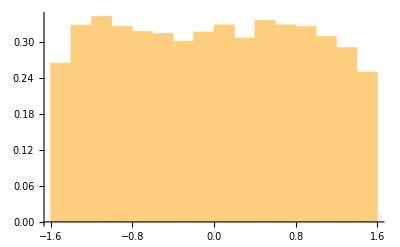
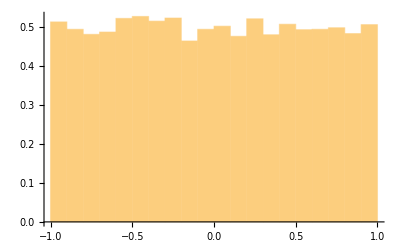

0.309356

```mathematica
randomRotation[n_]:=Module[{},
z=RandomVariate[NormalDistribution[0,1],{n,n}];
{q,r}=QRDecomposition[z];
d=Diagonal[r];
ph=d/Abs[d];
q*ph
];

n=3;
points=Table[randomRotation[n].{0,0,1},{10^4}];
Graphics3D[{{Gray,PointSize[Small],Point[points]},{Red,Thick,Arrow[{{0,0,0},{0,0,1}}]}},Axes->True]
{x,y,z}=Transpose@points;
ϕ=ArcTan[y/x];
Histogram[#,20,PDF]&/@{ϕ,x}
DistributionFitTest[Transpose[{ϕ,z}],UniformDistribution[{{-Pi/2,Pi/2},{-1,1}}]]
```

## Simple Newton

```mathematica
generateX[n_,e_,dsize_]:=Module[{wt,mean,cov,normal,X},
SeedRandom[0];
mean=Table[0,{n}];
cov=IdentityMatrix[n]*e+Array[1-e&,{n,n}];
normal=MultinormalDistribution[mean,cov];
X=RandomVariate[normal,{dsize}]//Transpose;
centerData[X]
];
```

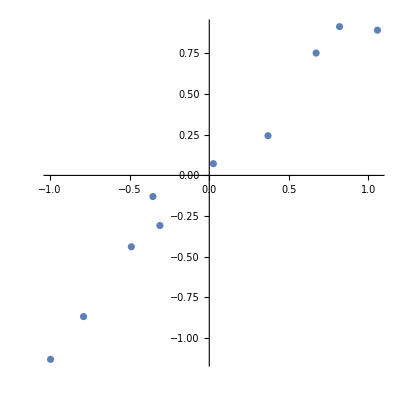

```mathematica
Clear[A,B,Bn,dW,W,X,Y,y,x,fs, subW,loss,err];
fs={10,2,2};
Export["~/git/whitening/exp/data/rotations_simple_fs.csv",fs];

X0=generateX[fs[[2]],0.01,fs[[1]]];
Export["~/git/whitening/exp/data/rotations_simple_X0.csv",X0];ListPlot[Transpose@X0,AspectRatio->1]

X=Array[W[0],{fs[[2]],fs[[1]]}];
X0=RandomReal[{0,1},{fs[[2]],fs[[1]]}];
subX:=(
Assert[Dimensions[X0]=={fs[[2]],fs[[1]]},"X mismatch"];Thread[Flatten@X->Flatten@X0]
);

Y=Array[y,{fs[[-1]],fs[[1]]}];
Y0=RandomReal[{0,1},{fs[[-1]],fs[[1]]}];
subY:=(
Assert[Dimensions[Y0]=={Last[fs], First[fs]},"Y mismatch"];
Thread[Flatten@Y->Flatten@Y0]
);

dsize=First@fs;
X0=generateX[fs[[2]],0.01,fs[[1]]];
n=Length[fs]-2;

makeW[k_]:=Array[W[k],{fs[[k+2]],fs[[k+1]]}];
makeInitializer[k_]:=RandomReal[{0,1},{fs[[k+2]],fs[[k+1]]}];
vars=Table[makeW[k],{k,1,n}];

varsf=Flatten[vectorize/@vars];
Ws=vars;
Wf=varsf;
subW[Wf0_]:=Thread[Wf->Wf0];
W0=Table[makeInitializer[k],{k,1,n}];
W0f=Flatten[vectorize/@W0];


W0=Table[makeInitializer[k],{k,1,n}];
errEq:=X-Fold[Dot,Reverse@vars].makeW[0];
lossEq:=Tr[1/(2 dsize)errEq.errEqᵀ];

(* A[i]=W[i-1]...W[0] = fprop needed to compute derivative at layer i *)
A[Wf_,1]:=makeW[0]/.subX;
A[Wf_,i_]:=Module[{},
makeW[i-1].A[Wf,i-1]/.subW[Wf]
];

(* B[i]=W[i+1]'...err = bprop needed to compute derivative at layer i *)
(* BB[i]=W[i+1]'...Identity = partial bprop needed for Newton's method *)
err[Ws_]:=Y-A[flatten@Ws,n+1]/.subY;
B[Wf_,n]:=err[unflatten[Wf]];
B[Wf_,i_]:=makeW[i+1]ᵀ.B[Wf,i+1]/.subW[Wf];
Bn[Wf_,n]:=IdentityMatrix[Last@fs];
Bn[Wf_,i_]:=makeW[i+1]ᵀ.Bn[Wf,i+1]/.subW[Wf];

dW[Wf_,i_]:=-B[Wf,i].A[Wf,i]ᵀ/dsize;

(* Define loss, gradient, Hessian *)
lossf[Wf_]:=(lossEq/.subW[Wf]/.subY/.subX);
loss[Ws_]:=lossf[flatten[Ws]];

gradEq=D[lossf[Wf],{Wf,1}];
hessEq=D[lossf[Wf],{Wf,2}];
gradf[Wf_]:=gradEq/.subW[Wf];
hessf[Wf_]:=hessEq/.subW[Wf];
hessBlock[W0f_,i_]:=
D[lossf[Wf],{c2v@vectorize@Ws[[i]],2}]/.subW[W0f]

ihessf[Wf_]:=PseudoInverse[hessf[Wf]];

Assert[hessBlock[W0f,1]==(A[W0f,1].A[W0f,1]ᵀ)⊗(Bn[W0f,1].Bn[W0f,1]ᵀ)/dsize,"hess check"];

Export["~/git/whitening/exp/data/rotations_simple_W0f.csv",W0f];
Export["~/git/whitening/exp/data/rotations_simple_fs.csv",fs];
Export["~/git/whitening/exp/data/rotations_simple_hess.csv",hessf[W0f]];
```

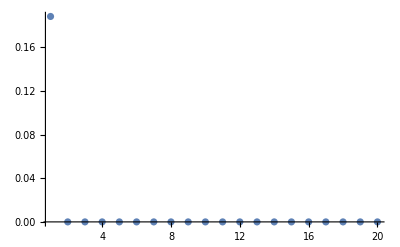

```mathematica
Clear[pointList,gradList,preList,lossList];
(* takes loss, grad, learning rate, produces list of losses *)
(* globals: points *)
optimizeNewton[lr_,w0f_,iters_]:=Module[{wf},
{pointList, gradList,preList, lossList}={{},{},{},{}};
wf=w0f;
For[iter=1,iter≤iters,iter++,
pointList=pointList~Append~wf;
gradList=gradList~Append~gradf[wf];
preList=preList~Append~ihessf[wf];
lossList=lossList~Append~lossf[wf];
wf=wf-lr*ihessf[wf].gradf[wf]
];
];
optimizeNewton[1.,W0f,20];
Export["~/git/whitening/exp/data/rotations_simple_losses_newton.csv",lossList];
ListPlot[lossList,PlotRange->All]
```

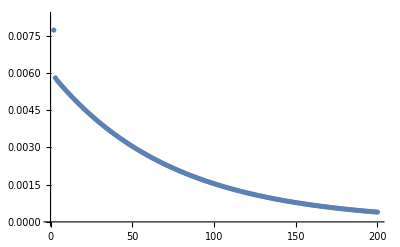

```mathematica
Clear[pointList,gradList,preList,lossList];
(* takes loss, grad, learning rate, produces list of losses *)
(* globals: points *)
optimizeSGD[lr_,w0f_,iters_]:=Module[{wf},
{pointList, gradList,preList, lossList}={{},{},{},{}};
wf=w0f;
For[iter=1,iter≤iters,iter++,
pointList=pointList~Append~wf;
gradList=gradList~Append~gradf[wf];
preList=preList~Append~ihessf[wf];
lossList=lossList~Append~lossf[wf];
wf=wf-lr*gradf[wf]
];
];
optimizeSGD[1.,W0f,200];
Export["~/git/whitening/exp/data/rotations_simple_losses_sgd.csv",lossList];
ListPlot[lossList]
```